```mathematica
(* Islands_Paper_PRA.nb -- 11/12/25 *)
```

```mathematica
Pherald[G_,etaT_]:= 4(etaT(G-1))^2/(etaT(G-1)+1)^6
TrueHeraldProbSame[G_,etaT_,Ni_]:=(1-(1-Pherald[G,etaT])^Ni)/2
TrueHeraldProbCross[G_,etaT_,Ni_]:=(1-2(1-Sqrt[Pherald[G,etaT]])^Ni+(1-Sqrt[Pherald[G,etaT]])^(2Ni))/2
```

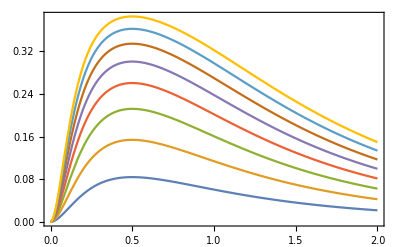

```mathematica
Plot[{TrueHeraldProbSame[1+dG,1,2],TrueHeraldProbSame[1+dG,1,4],TrueHeraldProbSame[1+dG,1,6],TrueHeraldProbSame[1+dG,1,8],TrueHeraldProbSame[1+dG,1,10],TrueHeraldProbSame[1+dG,1,12],TrueHeraldProbSame[1+dG,1,14],TrueHeraldProbSame[1+dG,1,16]},{dG,0,2},Frame->True]
```

```mathematica
PrIslandCorrect[G_,etaT_,etaR_]:=(NsP[G,etaT,etaR]^4/2)(2(1-NsP[G,etaT,etaR])^2-(2etaR /Ns[G,etaT])(3NsP[G,etaT,etaR]^3-5NsP[G,etaT,etaR]^2+2NsP[G,etaT,etaR])+(etaR^2/Ns[G,etaT]^2)(2NsP[G,etaT,etaR]^2-6NsP[G,etaT,etaR]^3+5NsP[G,etaT,etaR]^4))
PrIslandError[G_,etaT_,etaR_]:=3(NsP[G,etaT,etaR]^4/2)(2(1-NsP[G,etaT,etaR])^2-(2etaR/Ns[G,etaT])(3NsP[G,etaT,etaR]^3-5NsP[G,etaT,etaR]^2+2NsP[G,etaT,etaR])+(etaR^2/Ns[G,etaT]^2)(2NsP[G,etaT,etaR]^2-6NsP[G,etaT,etaR]^3+4NsP[G,etaT,etaR]^4))
BellFidelityR[G_,etaT_,etaR_]:= PrIslandCorrect[G,etaT,etaR]/(PrIslandCorrect[G,etaT,etaR]+PrIslandError[G,etaT,etaR])
BellFractionR[G_,etaT_,etaR_]:=(PrIslandCorrect[G,etaT,etaR] + PrIslandError[G,etaT,etaR])/(1- 2NsP[G,etaT,etaR]^2(1-etaR NsP[G,etaT,etaR]/(2Ns[G,etaT]))^2 + NsP[G,etaT,etaR]^4(1-etaR NsP[G,etaT,etaR]/Ns[G,etaT])^2)
BellFractionT[G_,etaT_]:=Ns[G,etaT]^6/(2-Ns[G,etaT^2])
BellPurityR[G_,etaT_,etaR_]:= (PrIslandCorrect[G,etaT,etaR]^2+3(PrIslandError[G,etaT,etaR]/3)^2)/((PrIslandCorrect[G,etaT,etaR]+PrIslandError[G,etaT,etaR])^2)
```

```mathematica
Ns[G_,etaT_]:=(etaT(G-1)+1)/G
NsP[G_,etaT_,etaR_]:=(etaR/Ns[G,etaT]+(1-etaR))^(-1)
```

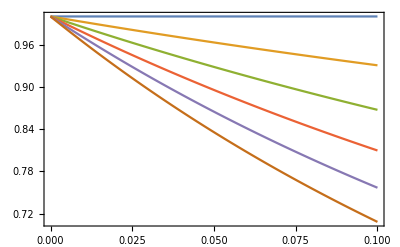

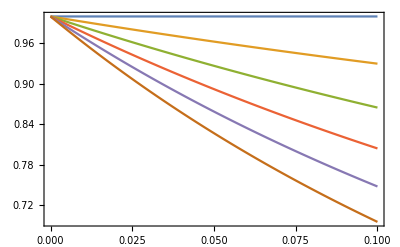

```mathematica
Plot[{BellFractionT[1+dG,1],BellFractionT[1+dG,0.9],BellFractionT[1+dG,0.8],BellFractionT[1+dG,0.7],BellFractionT[1+dG,0.6],BellFractionT[1+dG,0.5]},{dG,0,0.1},Frame->True]
Plot[{BellFractionR[1+dG,1,1],BellFractionR[1+dG,0.9,1],BellFractionR[1+dG,0.8,1],BellFractionR[1+dG,0.7,1],BellFractionR[1+dG,0.6,1],BellFractionR[1+dG,0.5,1]},{dG,0,0.1},Frame->True]
```

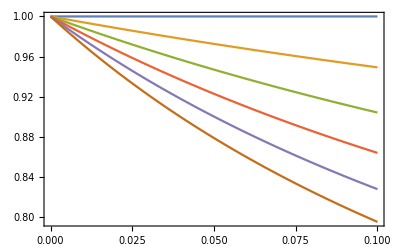

```mathematica
Plot[{BellFidelityR[1+dG,1,0.01],BellFidelityR[1+dG,0.9,0.01],BellFidelityR[1+dG,0.8,0.01],BellFidelityR[1+dG,0.7,0.01],BellFidelityR[1+dG,0.6,0.01],BellFidelityR[1+dG,0.5,0.01]},{dG,0,0.1},Frame->True]
```

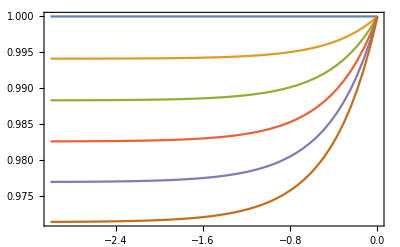

```mathematica
Plot[{BellFidelityR[1.01,1,10^lgEtaR],BellFidelityR[1.01,0.9,10^lgEtaR],BellFidelityR[1.01,0.8,10^lgEtaR],BellFidelityR[1.01,0.7,10^lgEtaR],
BellFidelityR[1.01,0.6,10^lgEtaR],BellFidelityR[1.01,0.5,10^lgEtaR]},{lgEtaR,-3,0},Frame->True]
```

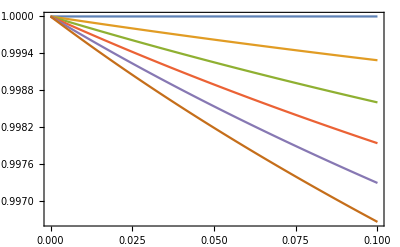

```mathematica
Plot[{BellFractionR[1+dG,1,0.01],BellFractionR[1+dG,0.9,0.01],BellFractionR[1+dG,0.8,0.01],BellFractionR[1+dG,0.7,0.01],BellFractionR[1+dG,0.6,0.01],BellFractionR[1+dG,0.5,0.01]},{dG,0,0.1},Frame->True]
```

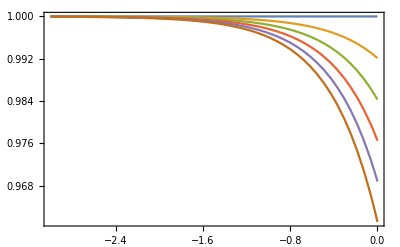

```mathematica
Plot[{BellFractionR[1.010,1,10^lgEtaR],BellFractionR[1.01,0.9,10^lgEtaR],BellFractionR[1.01,0.8,10^lgEtaR],
BellFractionR[1.01,0.7,10^lgEtaR],BellFractionR[1.01,0.6,10^lgEtaR],BellFractionR[1.01,0.5,10^lgEtaR]},{lgEtaR,-3,0},Frame->True, PlotRange->All]
```

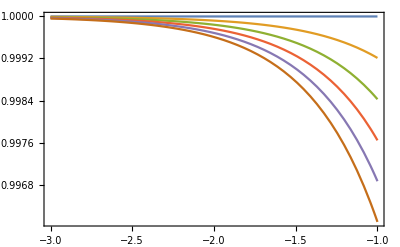

```mathematica
Plot[{BellFractionR[1.010,1,10^lgEtaR],BellFractionR[1.01,0.9,10^lgEtaR],BellFractionR[1.01,0.8,10^lgEtaR],
BellFractionR[1.01,0.7,10^lgEtaR],BellFractionR[1.01,0.6,10^lgEtaR],BellFractionR[1.01,0.5,10^lgEtaR]},{lgEtaR,-3,-1},Frame->True, PlotRange->All]
```

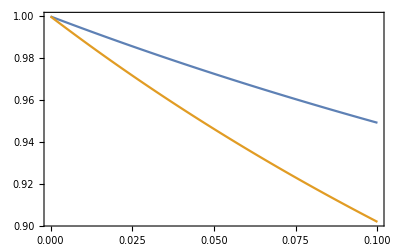

```mathematica
Plot[{BellFidelityR[1+dG,0.9,0.01],BellPurityR[1+dG,0.9,0.01]},{dG,0,0.1},Frame->True,PlotRange->All]
```

```mathematica
dGt[b_,etaT_]:=ArgMin[{Abs[BellFractionT[1+dG,etaT]-b],dG>0},dG]
```

```mathematica
Table[{etaT,dGt[0.99,etaT]},{etaT,0.9,0.5,-0.1}]
```

{{0.9,0.0128834},{0.8,0.00648281},{0.7,0.00436865},{0.6,0.003316},{0.5,0.00268639}}

```mathematica
Table[{Ni,TrueHeraldProbSame[1+0.0128834,0.9,Ni]},{Ni,1380,1390}]
```

{{1380,0.249892},{1381,0.250017},{1382,0.250143},{1383,0.250268},{1384,0.250393},{1385,0.250519},{1386,0.250644},{1387,0.250769},{1388,0.250894},{1389,0.251019},{1390,0.251144}}

```mathematica
Table[{Ni,TrueHeraldProbCross[1+0.0128834,0.9,Ni]},{Ni,50,60}]
```

{{50,0.22976},{51,0.234677},{52,0.239535},{53,0.244332},{54,0.249068},{55,0.253741},{56,0.258352},{57,0.2629},{58,0.267384},{59,0.271804},{60,0.276161}}

```mathematica
Table[{Ni,TrueHeraldProbCross[1+0.00648281,0.8,Ni]},{Ni,110,120}]
```

{{110,0.228963},{111,0.231203},{112,0.23343},{113,0.235646},{114,0.237849},{115,0.240039},{116,0.242218},{117,0.244383},{118,0.246536},{119,0.248676},{120,0.250804}}

```mathematica
Table[{Ni,TrueHeraldProbCross[1+0.00436865,0.7,Ni]},{Ni,200,210}]
```

{{200,0.247466},{201,0.248732},{202,0.249993},{203,0.25125},{204,0.252502},{205,0.25375},{206,0.254993},{207,0.256232},{208,0.257466},{209,0.258695},{210,0.259921}}

```mathematica
dGt[0.99,0.95]
```

0.025935

```mathematica
Table[{Ni,TrueHeraldProbCross[1+0.025935,0.95,Ni]},{Ni,20,30}]
```

{{20,0.185138},{21,0.196211},{22,0.207077},{23,0.217718},{24,0.22812},{25,0.238272},{26,0.248165},{27,0.257793},{28,0.26715},{29,0.276234},{30,0.285044}}

```mathematica
dGr[fid_,etaT_,etaR_]:=ArgMin[{Abs[BellFidelityR[1+dG,etaT,etaR]-fid],dG>0},dG]
```

```mathematica
Table[{etaT,dGr[0.99,etaT,0.01]},{etaT,0.9,0.5,-0.1}]
```

{{0.9,0.017329},{0.8,0.00859006},{0.7,0.00571035},{0.6,0.00427666},{0.5,0.0034184}}

```mathematica
Table[{Ni,TrueHeraldProbCross[1+0.017329,0.9,Ni]},{Ni,40,50}]
```

{{40,0.246092},{41,0.252366},{42,0.258528},{43,0.264579},{44,0.270516},{45,0.276339},{46,0.282048},{47,0.287643},{48,0.293123},{49,0.29849},{50,0.303744}}

```mathematica
Table[{Ni,TrueHeraldProbCross[1+0.00859006,0.8,Ni]},{Ni,90,100}]
```

{{90,0.24836},{91,0.251169},{92,0.253956},{93,0.256721},{94,0.259463},{95,0.262182},{96,0.264879},{97,0.267553},{98,0.270204},{99,0.272832},{100,0.275437}}

```mathematica
dGr[0.99,0.95,0.01]
```

0.0352691

```mathematica
Table[{Ni,TrueHeraldProbCross[1+0.0352691,0.95,Ni]},{Ni,10,20}]
```

{{10,0.108298},{11,0.123928},{12,0.139568},{13,0.155105},{14,0.170445},{15,0.185513},{16,0.200247},{17,0.2146},{18,0.228534},{19,0.242021},{20,0.255042}}

```mathematica
1-BellFractionR[1+0.0352691,0.95,0.01]
```

0.000135694

```mathematica
BellFractionR[1+0.0352691,0.95,0.01]
```

0.999864

```mathematica
1-BellFractionR[1+0.017329,0.9,0.01]
1-BellFractionR[1+0.00859006,0.8,0.01]
```

0.000135695

0.000135695

```mathematica
BellFractionR[1+0.017329,0.9,0.01]
BellFractionR[1+0.00859006,0.8,0.01]
```

0.999864

0.999864

```mathematica
PrIslandCorrect[1+0.017329,0.9,1]
```

0.494912

```mathematica
PrIslandCorrect[1+0.017329,0.9,0.01]
```

0.0000503334

```mathematica
DeliveryRate[dG_,etaT_,etaR_,Ni_,PulseRate_]:=PulseRate 2TrueHeraldProbCross[1+dG,etaT,Ni]PrIslandCorrect[1+dG,etaT,etaR]
```

```mathematica
DeliveryRate[0.017329,0.9,0.01,41,10^(10)]
```

254049.

```mathematica
DeliveryRate[0.00859006,0.8,0.01,91,10^(10)]
```

252844.

```mathematica
DeliveryRate[0.0352691,0.95,0.01,20,10^(10)]
```

256743.

```mathematica
BellPurityR[1+0.017329,0.9, 0.01]
```

0.980133

```mathematica
Df[lam_,Dt_,Dr_,L_]:=(Pi Dt Dr/(4lam L))^2
Df[1.55 10^{-6},0.1,1,1.5 10^6]
```

{0.00114113}

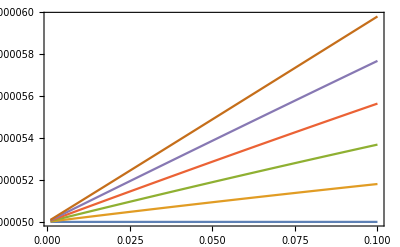

```mathematica
Plot[{PrIslandCorrect[1+dG,1,0.01],PrIslandCorrect[1+dG,0.9,0.01],PrIslandCorrect[1+dG,0.8,0.01],PrIslandCorrect[1+dG,0.7,0.01],PrIslandCorrect[1+dG,0.6,0.01],PrIslandCorrect[1+dG,0.5,0.01]},{dG,0.001,0.1},Frame->True]
```